# B_out for general translation of applied magnetic field

This file is cross referenced with Section F(f) of my notes. Please refer to notes for detailed explanations of the below calculations.

## Calculation for Spheroid: r(θ) =R-ϵ Cos[2θ]

```mathematica
Clear["Global`*"]
```

## Defining the parameters

```mathematica
bz = Symbol["bz"];(*Magnetic field gradient*)
dz = Symbol["dz"]; (*Displacement in z direction*)
dx = Symbol["dx"]; (*Displacement in x direction*)
dy = Symbol["dy"]; (*Displacement in y direction*)
R = Symbol["R"];
a=R+ϵ;  (*Equatorial radius*)
c=R-ϵ;  (*Polar radius*)
```

## Defining the equation of ellipsoid, considering R >> ϵ

```mathematica
rSp[θ_]=FullSimplify[(a  c)/Sqrt[c^2  Sin[θ]^2+a^2  Cos[θ]^2], ϵ^2==0];
(*Eqn. 1f*)
rSpheroid[θ_]=FullSimplify[Normal[Series[R^2(R (R+2 ϵ Cos[2 θ]))^(-1/2),{R, Infinity, 2}]],  ϵ^2==0]
```

R-ϵ Cos[2 θ]

## Position Vector for the ellipsoid can be defined as -

```mathematica
(*Eqn. 2f*)
vsph[θ_, ϕ_]= (R-ϵ Cos[2 θ])er[θ, ϕ] (*Position Vector*)
```

(R-ϵ Cos[2 θ]) er[θ,ϕ]

```mathematica
Table[Table[h[i, j] = Integrate[Conjugate[SphericalHarmonicY[i, j, θ, ϕ]]Sin[θ] (R-2 ϵ Cos[2 θ]), {θ, 0, π}, {ϕ, 0, 2π}], {j, 0, i}],{i, 0,4}]
```

{{2/3 √π (3 R+2 ϵ)},{0,0},{-16/3 √(π/5) ϵ,0,0},{0,0,0,0},{0,0,0,0,0}}

## Normal Vector at surface of spheroid can be written as -

This section contains the code for calculating the Normal vector to the Surface of Spheroid which is described in Detail in “Normal Vector to Surface of Spheroid.nb” or Section B(b) of my notes. Please refer to them for detailed explanations of the below calculations.

```mathematica
vsphθ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {θ}]]
vsphϕ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {ϕ}]]
finvsphθ[ θ_, ϕ_]=Collect[vsphθ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
finvsphϕ[ θ_, ϕ_]=Collect[vsphϕ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
eθ[θ,ϕ] = {0, 1, 0};
er[θ,ϕ] = {1, 0, 0};
eϕ[θ,ϕ] = {0, 0, 1};
finalvsphθ[ θ_, ϕ_]:=finvsphθ[ θ, ϕ]
finalvsphϕ[ θ_, ϕ_]:=finvsphϕ[ θ, ϕ]
nvsph[ θ_, ϕ_]:= Cross[finalvsphθ[θ, ϕ], finalvsphϕ[θ, ϕ]]
nvsph[ θ, ϕ]//FullSimplify
nnvsph[θ_, ϕ_]=Simplify[Refine[Normalize[nvsph[θ, ϕ]], {(R-ϵ Cos[2 θ])^2 Sin[θ]>0}]]
```

{(R-ϵ Cos[2 θ])^2 Sin[θ],4 ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2,0}

{((R-ϵ Cos[2 θ])^2 Sin[θ])/(√(16 Abs[ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2]^2+(R-ϵ Cos[2 θ])^4 Sin[θ]^2)),-(4 ϵ Cos[θ] (R-ϵ Cos[2 θ]) Sin[θ]^2)/(√(16 Abs[ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2]^2+(R-ϵ Cos[2 θ])^4 Sin[θ]^2)),0}

### Simplified Normal vector without any prior assumptions -

```mathematica
(*Eqn. 3f*)
Simplifiednormal[θ_, ϕ_]= {(R-ϵ Cos[2 θ])/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2)),-(2 ϵ Sin[2 θ])/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2)),0}
```

{(R-ϵ Cos[2 θ])/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2)),-(2 ϵ Sin[2 θ])/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2)),0}

## Defining the Magnetic field B_0

```mathematica
(*Eqn. 4f*)
B[x_,y_,z_]:=(1/2 )bz {x+dx,y+dy,-2(z+dz)}; 
(*Eqn. 5f*)
Div[B[x, y, z],{x, y, z}]

(*Eqn. 6f-7f*)
BSpherical[r_, θ_,ϕ_]:=Module[{x,y,z,er,etheta,ephi},x=r Sin[θ] Cos[ϕ];
y=r Sin[θ] Sin[ϕ];
z=r Cos[θ];
er={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
etheta={Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],-Sin[θ]};
ephi={-Sin[ϕ],Cos[ϕ],0};
{(B[x,y,z].er),(B[x,y,z].etheta),(B[x,y,z].ephi)}]
B0Spherical[r_, θ_,ϕ_]:=FullSimplify[BSpherical[r, θ, ϕ]]
B0Spherical[r, θ,ϕ]
```

0

{1/2 bz (-2 dz Cos[θ]-2 r Cos[θ]^2+Sin[θ] (dx Cos[ϕ]+r Sin[θ]+dy Sin[ϕ])),bz dz Sin[θ]+1/2 bz Cos[θ] (dx Cos[ϕ]+3 r Sin[θ]+dy Sin[ϕ]),1/2 bz (dy Cos[ϕ]-dx Sin[ϕ])}

## Boundary Condition -

We define the boundary condition as B_out(r, θ, ϕ).n(θ, ϕ) = 0
This equation can further be broken into left hand side (lhs) and right hand side (rhs) which should be equal to zero at surface of the spheroid. 
LHS = B_0(r, θ, ϕ).n(θ, ϕ)
RHS = Grad Φ(r, θ, ϕ).n(θ, ϕ)

## Calculating the left hand side of Boundary Condition B_0(r, θ, ϕ).n(θ, ϕ)

```mathematica
(*Eqn. 8f*)
LhsBCvsph[θ_, ϕ_]= Dot[B0Spherical[rSpheroid[θ],θ, ϕ], Simplifiednormal[θ, ϕ]]/.{ϵ->R s}
```

(bz (R-R s Cos[2 θ]) (-4 dz Cos[θ]+(1+3 Cos[2 θ]) (-R+R s Cos[2 θ])+2 dx Cos[ϕ] Sin[θ]+2 dy Sin[θ] Sin[ϕ]))/(4 √((R-R s Cos[2 θ])^2+4 R^2 s^2 Sin[2 θ]^2))-(bz R s Sin[2 θ] (2 dz Sin[θ]-3/4 R s Sin[4 θ]+Cos[θ] (dx Cos[ϕ]+3 R Sin[θ]+dy Sin[ϕ])))/(√((R-R s Cos[2 θ])^2+4 R^2 s^2 Sin[2 θ]^2))

### Approximating it by taylor expanding it upto first order

```mathematica
(*Eqn. 9f*)
AppLHSBCvsph[θ_, ϕ_]= FullSimplify[Refine[Normal[Series[LhsBCvsph[θ, ϕ], {s, 0, 1}]], {R>0}]]
```

-1/4 bz (R-R Cos[2 θ] (-3+s+3 s Cos[2 θ])+4 Cos[θ] (dz+4 dz s Sin[θ]^2)-2 Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ])+8 s Cos[θ]^2 Sin[θ] (dx Cos[ϕ]+3 R Sin[θ]+dy Sin[ϕ]))

### Verification that the above equation has a finite integral or not : Passed

```mathematica
(*Eqn. 10f*)
Integrate[AppLHSBCvsph[θ,ϕ]Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-32/15 bz π R s

### Evaluating the coefficients of the LHS part

```mathematica
(*Eqn. 11f*)
Table[Table[b[l, k] = Integrate[Conjugate[SphericalHarmonicY[l, k, θ, ϕ]]AppLHSBCvsph[θ, ϕ]Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}], {k, 0, l}],{l, 0, 5}]
```

{{-16/15 bz √π R s},{-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{-2/21 bz √(π/5) R (21+11 s),0,0},{16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
(*Eqn. 12f*)aaa ={{-16/15 bz √π R s},{-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{-2/21 bz √(π/5) R (21+11 s),0,0},{16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0}};
```

```mathematica
Table[Table[q[i, j]= aaa[[i+1]][[j+1]], {j, 0, i}], {i, 0, 5}]
```

{{-16/15 bz √π R s},{-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{-2/21 bz √(π/5) R (21+11 s),0,0},{16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0}}

### Final LHS all coefficients

```mathematica
(*Eqn. 13f-15f*)
Table[Table[If[j<0,b[i, j]=(-1)^j Refine[Conjugate[q[i, -j]], {Element[{bz, R, s, α, dz,dx, dy}, Reals]}], b[i, j]=q[i, j]], {j, -i, i}], {i, 0, 5}]
```

{{-16/15 bz √π R s},{-1/5 bz (dx+ⅈ dy) √(π/6) (-5+4 s),-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{0,0,-2/21 bz √(π/5) R (21+11 s),0,0},{0,0,-8/5 bz (dx+ⅈ dy) √(π/21) s,16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{0,0,0,0,48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

### Verification that all non zero coefficients are included

```mathematica
(*Eqn. 16f*)
FullSimplify[Sum[Sum[b[l, k]SphericalHarmonicY[l, k, θ, ϕ], {k, -l, l}],{l, 0, 5}]-AppLHSBCvsph[θ, ϕ]]
```

0

## Grad Phi term Calculation - Defining the induced magnetic field

```mathematica
PhiOut[r_,θ_,ϕ_, Nmax_]:=Sum[r^-(n+1)*Sum[g[n,m]* SphericalHarmonicY[n, m, θ, ϕ],{m,-n,n}],{n,0,Nmax}]
(*Eqn. 19f*)
PhiOut[r,θ,ϕ, Nmax]
```

∑_(n=0)^Nmax r^(-1-n) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]

#### Taking the gradient of induced magnetic field in spherical coordinates

```mathematica
(*Eqn. 20f*)
gradph[r_, θ_, ϕ_, Nmax_] = Grad[PhiOut[r, θ, ϕ, Nmax], {r, θ, ϕ}, "Spherical"]
```

{∑_(n=0)^Nmax (-r^(-2-n)-n r^(-2-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ],(∑_(n=0)^Nmax r^(-1-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))/r,(Csc[θ] ∑_(n=0)^Nmax r^(-1-n) ∑_(m=-n)^n ⅈ m g[n,m] SphericalHarmonicY[n,m,θ,ϕ])/r}

## Calculating the RHS part of the BC -

#### Taking the dot product of Grad PHI and normalized normal vector which forms the right hand side of the calculation

```mathematica
(*Eqn. 21f - Part 1*)
rhsbcvsph[θ_, ϕ_, Nmax_]= FullSimplify[Dot[gradph[rSpheroid[θ], θ, ϕ, Nmax], Simplifiednormal[θ, ϕ]]]
```

((R-ϵ Cos[2 θ])^2 ∑_(n=0)^Nmax (-(R-ϵ Cos[2 θ])^(-2-n)-n (R-ϵ Cos[2 θ])^(-2-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]-2 ϵ Sin[2 θ] ∑_(n=0)^Nmax (R-ϵ Cos[2 θ])^(-1-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))/((R-ϵ Cos[2 θ]) √((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2))

#### Simplifying the above equation by cancelling (R-ϵ Cos[2 θ]) from numerator and denominator

```mathematica
(*Eqn. 21f - Part 2*)SimplifiedRhsBC[θ_, ϕ_, Nmax_]= ((R-ϵ Cos[2 θ]) ∑_(n=0)^Nmax (-(R-ϵ Cos[2 θ])^(-2-n)-n (R-ϵ Cos[2 θ])^(-2-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]-4 ϵ Cos[θ] Sin[θ] ∑_(n=0)^Nmax (R-ϵ Cos[2 θ])^(-2-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))/( √((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2))
```

1/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2))((R-ϵ Cos[2 θ]) ∑_(n=0)^Nmax (-(R-ϵ Cos[2 θ])^(-2-n)-n (R-ϵ Cos[2 θ])^(-2-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]-4 ϵ Cos[θ] Sin[θ] ∑_(n=0)^Nmax (R-ϵ Cos[2 θ])^(-2-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))

### Simplifying it by multiplying the remaining (R-ϵ Cos[2 θ]) in the first part of the above expression

```mathematica
(*Eqn. 21f - Part 3*)moreSimplifiedRhsBC[θ_, ϕ_, Nmax_] = ((∑_(n=0)^Nmax (-(R-ϵ Cos[2 θ])^(-1-n)-n (R-ϵ Cos[2 θ])^(-1-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]-4 ϵ Cos[θ] Sin[θ] ∑_(n=0)^Nmax (R-ϵ Cos[2 θ])^(-2-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))/(√((R-ϵ Cos[2 θ])^2+4 ϵ^2 Sin[2 θ]^2)))/.{ϵ->R s}
```

1/(√((R-R s Cos[2 θ])^2+4 R^2 s^2 Sin[2 θ]^2))(∑_(n=0)^Nmax (-(R-R s Cos[2 θ])^(-1-n)-n (R-R s Cos[2 θ])^(-1-n)) ∑_(m=-n)^n g[n,m] SphericalHarmonicY[n,m,θ,ϕ]-4 R s Cos[θ] Sin[θ] ∑_(n=0)^Nmax (R-R s Cos[2 θ])^(-2-n) ∑_(m=-n)^n g[n,m] (m Cot[θ] SphericalHarmonicY[n,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+n] √Gamma[2+m+n] SphericalHarmonicY[n,1+m,θ,ϕ])/(√Gamma[-m+n] √Gamma[1+m+n])))

### Taylor Expanding it upto first order

```mathematica
(*Eqn. 22f*)AppRHSBC[θ_, ϕ_]=Collect[Refine[Normal[Series[moreSimplifiedRhsBC[θ, ϕ, 10],{s, 0, 1}]]/.{g[2, -2]->0,g[2, 2]->0,g[3,3]->0,g[3,-3]->0,g[3, -2]->0,g[3, 2]->0,g[4, -2]->0,g[4, 2]->0,g[4,-4]->0,g[4,-3]->0 ,g[4,3]->0,g[4,4]->0,g[5, -2]->0,g[5, 2]->0,g[5,-5]->0,g[5,-4]->0,g[5,-3]->0,g[5,3]->0,g[5,4]->0,g[5,5]->0, g[6,-6]->0,g[6,-5]->0,g[6,-4]->0,g[6,-3]->0,g[6, -2]->0,g[6, 2]->0,g[6,3]->0, g[6,4]->0,g[6,5]->0,g[6,6]->0,g[7,-7]->0,g[7,-6]->0,g[7,-5]->0,g[7,-4]->0,g[7,-3]->0,g[7, -2]->0,g[7, 2]->0, g[7,3]->0,g[7,4]->0,g[7,5]->0,g[7,6]->0,g[7,7]->0, g[8,-8]->0,g[8,-7]->0, g[8,-6]->0,g[8,-5]->0,g[8,-4]->0,g[8,-3]->0,g[8, -2]->0,g[8, 2]->0,g[8,3]->0,g[8,4]->0,g[8,5]->0,g[8,6]->0,g[8,7]->0,g[8,8] ->0,g[9,-9]->0,g[9,-8]->0,g[9,-7]->0, g[9,-6]->0,g[9,-5]->0,g[9,-4]->0,g[9,-3]->0,g[9, -2]->0,g[9, 2]->0,g[9,3]->0,g[9,4]->0,g[9,5]->0,g[9,6]->0,g[9,7]->0,g[9,8] ->0,g[9,9]->0,g[10,-10]->0,g[10,-9]->0,g[10,-8]->0,g[10,-7]->0, g[10,-6]->0,g[10,-5]->0,g[10,-4]->0,g[10,-3]->0,g[10, -2]->0,g[10, 2]->0,g[10,3]->0,g[10,4]->0,g[10,5]->0,g[10,6]->0,g[10,7]->0,g[10,8] ->0,g[10,9]->0, g[10,10]->0}, R>0],ⅇ^(ⅈ ϕ)] ;
```

```mathematica
(*Eqn. 23f*)
Table[Table[qq[l, k] = Integrate[Conjugate[SphericalHarmonicY[l, k, θ, ϕ]]AppRHSBC[θ, ϕ]Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}], {k, 0, 1}],{l, 7, 10}]
```

$Aborted

### Coefficients of RHS

```mathematica
(*Eqn. 25f*)tablegd = {{((-3+2 s) g[0,0])/(3 R^2)-(8 s g[2,0])/(√5 R^4)},{(14 R^2 (-5+s) g[1,0]-48 √21 s g[3,0])/(35 R^5),(14 R^2 (-5+7 s) g[1,1]-48 √14 s g[3,1])/(35 R^5)},{(-56 √5 R^4 s g[0,0]+15 R^2 (-21+4 s) g[2,0]-480 √5 s g[4,0])/(105 R^6),(3 R^2 (-21+16 s) g[2,1]-80 √6 s g[4,1])/(21 R^6),0},{-(4 (792 √21 R^4 s g[1,0]-77 R^2 (-45+7 s) g[3,0]+1500 √77 s g[5,0]))/(3465 R^7),-(4 (264 √14 R^4 s g[1,1]-77 R^2 (-15+8 s) g[3,1]+150 √770 s g[5,1]))/(1155 R^7),0,0},{-(128 s g[2,0])/(7 √5 R^4)+(5 (-77+10 s) g[4,0])/(77 R^6)-(840 s g[6,0])/(11 √13 R^8),(-9152 √6 R^4 s g[2,1]+39 R^2 (-385+158 s) g[4,1]-1176 √2730 s g[6,1])/(3003 R^8),0,0,0},{-(1040 s g[3,0])/(9 √77 R^5)+(2 (-9+s) g[5,0])/(3 R^7)-(1568 √(3/55) s g[7,0])/(13 R^9),-(104 √(10/77) s g[3,1])/(3 R^5)+(2 (-3+s) g[5,1])/R^7-(448 √(7/11) s g[7,1])/(13 R^9),0,0,0,0},{-(760 s g[4,0])/(11 √13 R^6)+(7 (-165+16 s) g[6,0])/(165 R^8)-(2688 s g[8,0])/(5 √221 R^10),-(152 √(70/39) s g[4,1])/(11 R^6)+((-385+108 s) g[6,1])/(55 R^8)-(576 √(21/221) s g[8,1])/(5 R^10),0,0,0,0,0}}
```

{{((-3+2 s) g[0,0])/(3 R^2)-(8 s g[2,0])/(√5 R^4)},{(14 R^2 (-5+s) g[1,0]-48 √21 s g[3,0])/(35 R^5),(14 R^2 (-5+7 s) g[1,1]-48 √14 s g[3,1])/(35 R^5)},{(-56 √5 R^4 s g[0,0]+15 R^2 (-21+4 s) g[2,0]-480 √5 s g[4,0])/(105 R^6),(3 R^2 (-21+16 s) g[2,1]-80 √6 s g[4,1])/(21 R^6),0},{-(4 (792 √21 R^4 s g[1,0]-77 R^2 (-45+7 s) g[3,0]+1500 √77 s g[5,0]))/(3465 R^7),-(4 (264 √14 R^4 s g[1,1]-77 R^2 (-15+8 s) g[3,1]+150 √770 s g[5,1]))/(1155 R^7),0,0},{-(128 s g[2,0])/(7 √5 R^4)+(5 (-77+10 s) g[4,0])/(77 R^6)-(840 s g[6,0])/(11 √13 R^8),(-9152 √6 R^4 s g[2,1]+39 R^2 (-385+158 s) g[4,1]-1176 √2730 s g[6,1])/(3003 R^8),0,0,0},{-(1040 s g[3,0])/(9 √77 R^5)+(2 (-9+s) g[5,0])/(3 R^7)-(1568 √(3/55) s g[7,0])/(13 R^9),-(104 √(10/77) s g[3,1])/(3 R^5)+(2 (-3+s) g[5,1])/R^7-(448 √(7/11) s g[7,1])/(13 R^9),0,0,0,0},{-(760 s g[4,0])/(11 √13 R^6)+(7 (-165+16 s) g[6,0])/(165 R^8)-(2688 s g[8,0])/(5 √221 R^10),-(152 √(70/39) s g[4,1])/(11 R^6)+((-385+108 s) g[6,1])/(55 R^8)-(576 √(21/221) s g[8,1])/(5 R^10),0,0,0,0,0}}

### Coefficients copied from the Spheroid rotation notebook

```mathematica
tablePrevious ={{((-3+2 s) g[0,0])/(3 R^2)-(8 s g[2,0])/(√5 R^4)},{(14 R^2 (-5+s) g[1,0]-48 √21 s g[3,0])/(35 R^5),(14 R^2 (-5+7 s) g[1,1]-48 √14 s g[3,1])/(35 R^5)},{(-56 √5 R^4 s g[0,0]+15 R^2 (-21+4 s) g[2,0]-480 √5 s g[4,0])/(105 R^6),(3 R^2 (-21+16 s) g[2,1]-80 √6 s g[4,1])/(21 R^6),0},{-(4 (792 √21 R^4 s g[1,0]-77 R^2 (-45+7 s) g[3,0]+1500 √77 s g[5,0]))/(3465 R^7),-(4 (264 √14 R^4 s g[1,1]-77 R^2 (-15+8 s) g[3,1]+150 √770 s g[5,1]))/(1155 R^7),0,0},{-(128 s g[2,0])/(7 √5 R^4)+(5 (-77+10 s) g[4,0])/(77 R^6)-(840 s g[6,0])/(11 √13 R^8),(-9152 √6 R^4 s g[2,1]+39 R^2 (-385+158 s) g[4,1]-1176 √2730 s g[6,1])/(3003 R^8),0,0,0},{-(1040 s g[3,0])/(9 √77 R^5)+(2 (-9+s) g[5,0])/(3 R^7)-(1568 √(3/55) s g[7,0])/(13 R^9),-(104 √(10/77) s g[3,1])/(3 R^5)+(2 (-3+s) g[5,1])/R^7-(448 √(7/11) s g[7,1])/(13 R^9),0,0,0,0},{-(760 s g[4,0])/(11 √13 R^6)+(7 (-165+16 s) g[6,0])/(165 R^8)-(2688 s g[8,0])/(5 √221 R^10),-(152 √(70/39) s g[4,1])/(11 R^6)+((-385+108 s) g[6,1])/(55 R^8)-(576 √(21/221) s g[8,1])/(5 R^10),0,0,0,0,0}};
```

### Verifying the previous table and new table are same or not (Passed - hence proved that expanding upto 8 is enough for calculation purposes)

```mathematica
tablePrevious==tablegd
```

True

### Final Coefficients for the RHS part of the BC -

```mathematica
(*Eqn. 26f RHS*)gcoeffRHS = {{((-3+2 s) g[0,0])/(3 R^2)-(8 s g[2,0])/(√5 R^4)},{(14 R^2 (-5+s) g[1,0]-48 √21 s g[3,0])/(35 R^5),(14 R^2 (-5+7 s) g[1,1]-48 √14 s g[3,1])/(35 R^5)},{(-56 √5 R^4 s g[0,0]+15 R^2 (-21+4 s) g[2,0]-480 √5 s g[4,0])/(105 R^6),(3 R^2 (-21+16 s) g[2,1]-80 √6 s g[4,1])/(21 R^6),0},{-(4 (792 √21 R^4 s g[1,0]-77 R^2 (-45+7 s) g[3,0]+1500 √77 s g[5,0]))/(3465 R^7),-(4 (264 √14 R^4 s g[1,1]-77 R^2 (-15+8 s) g[3,1]+150 √770 s g[5,1]))/(1155 R^7),0,0},{-(128 s g[2,0])/(7 √5 R^4)+(5 (-77+10 s) g[4,0])/(77 R^6)-(840 s g[6,0])/(11 √13 R^8),(-9152 √6 R^4 s g[2,1]+39 R^2 (-385+158 s) g[4,1]-1176 √2730 s g[6,1])/(3003 R^8),0,0,0},{-(1040 s g[3,0])/(9 √77 R^5)+(2 (-9+s) g[5,0])/(3 R^7)-(1568 √(3/55) s g[7,0])/(13 R^9),-(104 √(10/77) s g[3,1])/(3 R^5)+(2 (-3+s) g[5,1])/R^7-(448 √(7/11) s g[7,1])/(13 R^9),0,0,0,0},{-(760 s g[4,0])/(11 √13 R^6)+(7 (-165+16 s) g[6,0])/(165 R^8)-(2688 s g[8,0])/(5 √221 R^10),-(152 √(70/39) s g[4,1])/(11 R^6)+((-385+108 s) g[6,1])/(55 R^8)-(576 √(21/221) s g[8,1])/(5 R^10),0,0,0,0,0}};
```

### Coefficients of LHS part -

```mathematica
(*Eqn. 26f LHS*)
bcoeffLHS ={{-16/15 bz √π R s},{-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{-2/21 bz √(π/5) R (21+11 s),0,0},{16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0}}
```

{{-16/15 bz √π R s},{-2/5 bz dz √(π/3) (5+8 s),1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)},{-2/21 bz √(π/5) R (21+11 s),0,0},{16/5 bz dz √(π/7) s,8/5 bz (dx-ⅈ dy) √(π/21) s,0,0},{48/35 bz √π R s,0,0,0,0},{0,0,0,0,0,0}}

## Comparing the Coefficients both the sides and Obtaining the g’s

### Solving g[0, 0], g[2, 0], g[4,0], g[6,0]

```mathematica
(*Eqn. 27f Part 1*)
Solve[((-3+2 s) g[0,0])/(3 R^2)-(8 s g[2,0])/(√5 R^4)==-16/15 bz √π R s && -(56 R^4 s g[0,0]+3 √5 R^2 (21-4 s) g[2,0]+480 s g[4,0])/(21 √5 R^6)==-2/21 bz √(π/5) R (21+11 s) && -(128 s g[2,0])/(7 √5 R^4)+(5 (-77+10 s) g[4,0])/(77 R^6)-(840 s g[6,0])/(11 √13 R^8)==48/35 bz √π R s && -(760 s g[4,0])/(11 √13 R^6)+(7 (-165+16 s) g[6,0])/(165 R^8)==0, {g[0,0], g[2,0], g[4,0], g[6, 0]}]
```

{{g[0,0]→(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),g[2,0]→(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),g[4,0]→-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),g[6,0]→-(547200 s^2 (-5 bz √(13 π) R^9+2 bz √(13 π) R^9 s+8 bz √(13 π) R^9 s^2))/(7 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4))}}

### Assigning the Values

```mathematica
{g[0,0],g[2,0],g[4,0],g[6,0]}={(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),-(547200 s^2 (-5 bz √(13 π) R^9+2 bz √(13 π) R^9 s+8 bz √(13 π) R^9 s^2))/(7 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4))}
```

{(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),-(547200 s^2 (-5 bz √(13 π) R^9+2 bz √(13 π) R^9 s+8 bz √(13 π) R^9 s^2))/(7 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4))}

### Solve g[1,0], g[3,0], g[5,0]

```mathematica
(*Eqn. 27f Part 2*)
Solve[(14 R^2 (-5+s) g[1,0]-48 √21 s g[3,0])/(35 R^5)==-2/5 bz dz √(π/3) (5+8 s) && -(4 (792 √21 R^4 s g[1,0]-77 R^2 (-45+7 s) g[3,0]+1500 √77 s g[5,0]))/(3465 R^7)== 16/5 bz dz √(π/7) s && -(1040 s g[3,0])/(9 √77 R^5)+(2 (-9+s) g[5,0])/(3 R^7)==0, {g[1,0], g[3,0], g[5,0]}]
```

{{g[1,0]→-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),g[3,0]→(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),g[5,0]→(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3)}}

### Assigning the Values

```mathematica
{g[1,0],g[3,0],g[5,0]}={-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3)}
```

{-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3)}

### Solve g[1,1], g[3,1], g[5,1]

```mathematica
(*Eqn. 28f*)
```

```mathematica
Solve[(14 R^2 (-5+7 s) g[1,1]-48 √14 s g[3,1])/(35 R^5)==1/5 bz (dx-ⅈ dy) √(π/6) (-5+4 s)&& -(4 (264 √14 R^4 s g[1,1]-77 R^2 (-15+8 s) g[3,1]+150 √770 s g[5,1]))/(1155 R^7)==8/5 bz (dx-ⅈ dy) √(π/21) s&& -(104 √(10/77) s g[3,1])/(3 R^5)+(2 (-3+s) g[5,1])/R^7==0, {g[1,1], g[3,1], g[5,1]}]
```

{{g[1,1]→(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),g[3,1]→-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),g[5,1]→-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3)}}

### Assigning the Values

```mathematica
{g[1,1],g[3,1],g[5,1]}={(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3)}
```

{(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3)}

## Final values of the coefficients of PHI term

### List of all the non zero non simplified coefficients in the PHIOut term

```mathematica
(*Eqn. 29f*)
glist = {g[0, 0], g[1, 0], g[2, 0], g[3, 0], g[4, 0], g[5, 0], g[6, 0],g[1,1], g[3,1],g[5,1]}
```

{(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3),-(547200 s^2 (-5 bz √(13 π) R^9+2 bz √(13 π) R^9 s+8 bz √(13 π) R^9 s^2))/(7 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3)}

### List of all the non zero non simplified coefficients with k = 0 in the PHIOut term

```mathematica
(*Eqn. 30f*)
g0 ={g[0, 0], g[1, 0], g[2, 0], g[3, 0], g[4, 0], g[5, 0], g[6, 0]}
```

{(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3),-(547200 s^2 (-5 bz √(13 π) R^9+2 bz √(13 π) R^9 s+8 bz √(13 π) R^9 s^2))/(7 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4))}

### List of all the non zero non simplified coefficients with k = 1 in the PHIOut term

```mathematica
(*Eqn. 31f*)
g1 ={g[1,1], g[3,1],g[5,1]}
```

{(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3)}

```mathematica
gall = Table[Table[g[j,i], {i, 0,j}], {j, 0, 5}]/.{g[2, -2]->0,g[2, 2]->0,g[3,3]->0,g[3,-3]->0,g[3, -2]->0,g[3, 2]->0,g[4, -2]->0,g[4, 2]->0,g[4,-4]->0,g[4,-3]->0 ,g[4,3]->0,g[4,4]->0,g[5, -2]->0,g[5, 2]->0,g[5,-5]->0,g[5,-4]->0,g[5,-3]->0,g[5,3]->0,g[5,4]->0,g[5,5]->0, g[2,1]->0, g[4,1]->0};
```

```mathematica
Table[Table[u[i, j]= gall[[i+1]][[j+1]], {j, 0, i}], {i, 0, 5}];
all =Table[Table[If[j<0,uu[i, j]=(-1)^j Refine[Conjugate[u[i, -j]], {Element[{bz, R, s, α, dz,dx, dy}, Reals]}], uu[i, j]=u[i, j]], {j, -i, i}], {i, 0, 5}]
```

{{(80 bz √π R^3 (-6435 s^2-76986 s^3+82144 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)},{-(35 bz (dx+ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3)),-(35 bz dz √(π/3) R^3 (-99-132 s+703 s^2+1336 s^3))/(3465-1617 s-40049 s^2+7033 s^3),(35 bz (dx-ⅈ dy) √(π/6) R^3 (99-165 s-548 s^2+544 s^3))/(2 (3465-7854 s-28783 s^2+38072 s^3))},{0,0,(6 (75075 bz √(5 π) R^5-27755 bz √(5 π) R^5 s-764820 bz √(5 π) R^5 s^2-25316 bz √(5 π) R^5 s^3+1555648 bz √(5 π) R^5 s^4))/(5 (675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4)),0,0},{0,0,(66 bz (dx+ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),(132 bz dz √(7 π) R^5 s (-9-8 s+s^2))/(3465-1617 s-40049 s^2+7033 s^3),-(66 bz (dx-ⅈ dy) √(3 π) s (3 √7 R^5-4 √7 R^5 s+√7 R^5 s^2))/(3465-7854 s-28783 s^2+38072 s^3),0,0},{0,0,0,0,-(624 (825 bz √π R^7 s-410 bz √π R^7 s^2-1288 bz √π R^7 s^3+128 bz √π R^7 s^4))/(675675-732420 s-12335580 s^2+9782256 s^3+9893632 s^4),0,0,0,0},{0,0,0,0,(104 bz (dx+ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3),(2080 s^2 (bz dz √(11 π) R^7+bz dz √(11 π) R^7 s))/(3465-1617 s-40049 s^2+7033 s^3),-(104 bz (dx-ⅈ dy) √(3 π) s^2 (-√110 R^7+√110 R^7 s))/(3465-7854 s-28783 s^2+38072 s^3),0,0,0,0}}

### Simplified Coefficients

```mathematica
gs =FullSimplify[Normal[Series[all , {s, 0, 1}]]]
```

{{0},{-1/10 bz (dx+ⅈ dy) √(π/6) R^3 (5+3 s),1/5 bz dz √(π/3) R^3 (5+9 s),1/10 bz (dx-ⅈ dy) √(π/6) R^3 (5+3 s)},{0,0,2/21 bz √(π/5) R^5 (7+5 s),0,0},{0,0,2/5 bz (dx+ⅈ dy) √((3 π)/7) R^5 s,-12/5 bz dz √(π/7) R^5 s,-2/5 bz (dx-ⅈ dy) √((3 π)/7) R^5 s,0,0},{0,0,0,0,-16/21 bz √π R^7 s,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

### List of all the non zero simplified coefficients in the PHIOut term

```mathematica
(*Eqn. 32f -33f*)
gg[0,0]=0;
gg[1,-1]=-1/10 bz (dx+ⅈ dy) √(π/6) R^3 (5+3 s);
gg[1,0]=1/5 bz dz √(π/3) R^3 (5+9 s);
gg[1,1]=1/10 bz (dx-ⅈ dy) √(π/6) R^3 (5+3 s);
gg[2,0]=2/21 bz √(π/5) R^5 (7+5 s);
gg[3,-1]=2/5 bz (dx+ⅈ dy) √((3 π)/7) R^5 s;
gg[3,0]=-12/5 bz dz √(π/7) R^5 s;
gg[3,1]=-2/5 bz (dx-ⅈ dy) √((3 π)/7) R^5 s;
gg[4,0]=-16/21 bz √π R^7 s;
```

```mathematica
Table[Table[gg[n,m], {m, -n, n}],{n,0,6}]
```

{{0},{-1/10 bz (dx+ⅈ dy) √(π/6) R^3 (5+3 s),1/5 bz dz √(π/3) R^3 (5+9 s),1/10 bz (dx-ⅈ dy) √(π/6) R^3 (5+3 s)},{gg[2,-2],gg[2,-1],2/21 bz √(π/5) R^5 (7+5 s),gg[2,1],gg[2,2]},{gg[3,-3],gg[3,-2],2/5 bz (dx+ⅈ dy) √((3 π)/7) R^5 s,-12/5 bz dz √(π/7) R^5 s,-2/5 bz (dx-ⅈ dy) √((3 π)/7) R^5 s,gg[3,2],gg[3,3]},{gg[4,-4],gg[4,-3],gg[4,-2],gg[4,-1],-16/21 bz √π R^7 s,gg[4,1],gg[4,2],gg[4,3],gg[4,4]},{gg[5,-5],gg[5,-4],gg[5,-3],gg[5,-2],gg[5,-1],gg[5,0],gg[5,1],gg[5,2],gg[5,3],gg[5,4],gg[5,5]},{gg[6,-6],gg[6,-5],gg[6,-4],gg[6,-3],gg[6,-2],gg[6,-1],gg[6,0],gg[6,1],gg[6,2],gg[6,3],gg[6,4],gg[6,5],gg[6,6]}}

### Passed the test for Sphere

```mathematica
gtest = all/.{s->0}
```

{{0},{-1/2 bz (dx+ⅈ dy) √(π/6) R^3,bz dz √(π/3) R^3,1/2 bz (dx-ⅈ dy) √(π/6) R^3},{0,0,2/3 bz √(π/5) R^5,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Table[gg[n,m], {m, -n, n}],{n,0,6}]/.{s->0}
```

{{0},{-1/2 bz (dx+ⅈ dy) √(π/6) R^3,bz dz √(π/3) R^3,1/2 bz (dx-ⅈ dy) √(π/6) R^3},{gg[2,-2],gg[2,-1],2/3 bz √(π/5) R^5,gg[2,1],gg[2,2]},{gg[3,-3],gg[3,-2],0,0,0,gg[3,2],gg[3,3]},{gg[4,-4],gg[4,-3],gg[4,-2],gg[4,-1],0,gg[4,1],gg[4,2],gg[4,3],gg[4,4]},{gg[5,-5],gg[5,-4],gg[5,-3],gg[5,-2],gg[5,-1],gg[5,0],gg[5,1],gg[5,2],gg[5,3],gg[5,4],gg[5,5]},{gg[6,-6],gg[6,-5],gg[6,-4],gg[6,-3],gg[6,-2],gg[6,-1],gg[6,0],gg[6,1],gg[6,2],gg[6,3],gg[6,4],gg[6,5],gg[6,6]}}

## Calculating the B_outfrom the above calculated simplified coefficients -

## Defining the PhiOut and Grad[PhiOut] with the evaluated coefficients

### Checking all the terms are encountered or not

```mathematica
PhiOutSpheroid[r_,θ_,ϕ_]=Sum[Sum[r^-(n+1)*gv[n,m]* SphericalHarmonicY[n, m, θ, ϕ],{m,-n,n}],{n, 0,4}]/.{gg[2,-2]->0,gg[2,-1]->0, gg[2,1]->0,gg[2,2]->0,gg[3,-3]->0,gg[3,-2]->0,gg[3,2]->0,gg[3,3]->0,gg[4,-4]->0,gg[4,-3]->0,gg[4,-2]->0,gg[4,-1]->0,gg[4,1]->0,gg[4,2]->0,gg[4,3]->0,gg[4,4]->0}
```

gv[0,0]/(2 √π r)+(√(3/π) Cos[θ] gv[1,0])/(2 r^2)+(√(5/π) (-1+3 Cos[θ]^2) gv[2,0])/(4 r^3)+(√(7/π) (-3 Cos[θ]+5 Cos[θ]^3) gv[3,0])/(4 r^4)+(3 (3-30 Cos[θ]^2+35 Cos[θ]^4) gv[4,0])/(16 √π r^5)+(ⅇ^(-ⅈ ϕ) √(3/(2 π)) gv[1,-1] Sin[θ])/(2 r^2)-(ⅇ^(ⅈ ϕ) √(3/(2 π)) gv[1,1] Sin[θ])/(2 r^2)+(ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] gv[2,-1] Sin[θ])/(2 r^3)-(ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] gv[2,1] Sin[θ])/(2 r^3)+(ⅇ^(-ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) gv[3,-1] Sin[θ])/(8 r^4)-(ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) gv[3,1] Sin[θ])/(8 r^4)+(3 ⅇ^(-ⅈ ϕ) √(5/π) Cos[θ] (-3+7 Cos[θ]^2) gv[4,-1] Sin[θ])/(8 r^5)-(3 ⅇ^(ⅈ ϕ) √(5/π) Cos[θ] (-3+7 Cos[θ]^2) gv[4,1] Sin[θ])/(8 r^5)+(ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) gv[2,-2] Sin[θ]^2)/(4 r^3)+(ⅇ^(2 ⅈ ϕ) √(15/(2 π)) gv[2,2] Sin[θ]^2)/(4 r^3)+(ⅇ^(-2 ⅈ ϕ) √(105/(2 π)) Cos[θ] gv[3,-2] Sin[θ]^2)/(4 r^4)+(ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] gv[3,2] Sin[θ]^2)/(4 r^4)+(3 ⅇ^(-2 ⅈ ϕ) √(5/(2 π)) (-1+7 Cos[θ]^2) gv[4,-2] Sin[θ]^2)/(8 r^5)+(3 ⅇ^(2 ⅈ ϕ) √(5/(2 π)) (-1+7 Cos[θ]^2) gv[4,2] Sin[θ]^2)/(8 r^5)+(ⅇ^(-3 ⅈ ϕ) √(35/π) gv[3,-3] Sin[θ]^3)/(8 r^4)-(ⅇ^(3 ⅈ ϕ) √(35/π) gv[3,3] Sin[θ]^3)/(8 r^4)+(3 ⅇ^(-3 ⅈ ϕ) √(35/π) Cos[θ] gv[4,-3] Sin[θ]^3)/(8 r^5)-(3 ⅇ^(3 ⅈ ϕ) √(35/π) Cos[θ] gv[4,3] Sin[θ]^3)/(8 r^5)+(3 ⅇ^(-4 ⅈ ϕ) √(35/(2 π)) gv[4,-4] Sin[θ]^4)/(16 r^5)+(3 ⅇ^(4 ⅈ ϕ) √(35/(2 π)) gv[4,4] Sin[θ]^4)/(16 r^5)

```mathematica
(*Eqn. 34f*)
PhiOutSpheroid[r_,θ_,ϕ_]=Sum[Sum[r^-(n+1)*gg[n,m]* SphericalHarmonicY[n, m, θ, ϕ],{m,-n,n}],{n, 0,4}]/.{gg[2,-2]->0,gg[2,-1]->0, gg[2,1]->0,gg[2,2]->0,gg[3,-3]->0,gg[3,-2]->0,gg[3,2]->0,gg[3,3]->0,gg[4,-4]->0,gg[4,-3]->0,gg[4,-2]->0,gg[4,-1]->0,gg[4,1]->0,gg[4,2]->0,gg[4,3]->0,gg[4,4]->0}
```

(bz dz R^3 (5+9 s) Cos[θ])/(10 r^2)+(bz R^5 (7+5 s) (-1+3 Cos[θ]^2))/(42 r^3)-(3 bz dz R^5 s (-3 Cos[θ]+5 Cos[θ]^3))/(5 r^4)-(bz R^7 s (3-30 Cos[θ]^2+35 Cos[θ]^4))/(7 r^5)-(bz (dx+ⅈ dy) ⅇ^(-ⅈ ϕ) R^3 (5+3 s) Sin[θ])/(40 r^2)-(bz (dx-ⅈ dy) ⅇ^(ⅈ ϕ) R^3 (5+3 s) Sin[θ])/(40 r^2)+(3 bz (dx+ⅈ dy) ⅇ^(-ⅈ ϕ) R^5 s (-1+5 Cos[θ]^2) Sin[θ])/(20 r^4)+(3 bz (dx-ⅈ dy) ⅇ^(ⅈ ϕ) R^5 s (-1+5 Cos[θ]^2) Sin[θ])/(20 r^4)

### Grad[PhiOut]

```mathematica
(*Eqn. 35f*)
GradPhiSpheroid[r_,θ_,ϕ_] = FullSimplify[Grad[PhiOutSpheroid[r, θ, ϕ], {r, θ, ϕ}, "Spherical"]]
```

{1/(280 r^6)bz R^3 (5 R^2 (45 R^2 s-2 r^2 (7+5 s))-56 dz r (-9 R^2 s+r^2 (5+9 s)) Cos[θ]+840 dz r R^2 s Cos[3 θ]+875 R^4 s Cos[4 θ]+28 r (-18 R^2 s+r^2 (5+3 s)) Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ])-10 R^2 Cos[2 θ] (-50 R^2 s+3 r^2 (7+5 s)+84 r s Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ]))),1/(140 r^6)bz R^3 (-7 dz r (-9 R^2 s+2 r^2 (5+9 s)) Sin[θ]+10 R^2 (10 R^2 s-r^2 (7+5 s)) Sin[2 θ]+315 dz r R^2 s Sin[3 θ]+350 R^4 s Sin[4 θ]-7 r Cos[θ] (21 R^2 s+r^2 (5+3 s)-45 R^2 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),(bz R^3 (9 R^2 s-r^2 (5+3 s)+15 R^2 s Cos[2 θ]) (dy Cos[ϕ]-dx Sin[ϕ]))/(20 r^5)}

### Final Expression of B_out for Spheroid

```mathematica
(*Eqn. 36f*)
BoutSpheroid[r_, θ_, ϕ_]= B0Spherical[r, θ, ϕ]-GradPhiSpheroid[r,θ,ϕ]
```

{1/2 bz (-2 dz Cos[θ]-2 r Cos[θ]^2+Sin[θ] (dx Cos[ϕ]+r Sin[θ]+dy Sin[ϕ]))-1/(280 r^6)bz R^3 (5 R^2 (45 R^2 s-2 r^2 (7+5 s))-56 dz r (-9 R^2 s+r^2 (5+9 s)) Cos[θ]+840 dz r R^2 s Cos[3 θ]+875 R^4 s Cos[4 θ]+28 r (-18 R^2 s+r^2 (5+3 s)) Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ])-10 R^2 Cos[2 θ] (-50 R^2 s+3 r^2 (7+5 s)+84 r s Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ]))),bz dz Sin[θ]+1/2 bz Cos[θ] (dx Cos[ϕ]+3 r Sin[θ]+dy Sin[ϕ])-1/(140 r^6)bz R^3 (-7 dz r (-9 R^2 s+2 r^2 (5+9 s)) Sin[θ]+10 R^2 (10 R^2 s-r^2 (7+5 s)) Sin[2 θ]+315 dz r R^2 s Sin[3 θ]+350 R^4 s Sin[4 θ]-7 r Cos[θ] (21 R^2 s+r^2 (5+3 s)-45 R^2 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),1/2 bz (dy Cos[ϕ]-dx Sin[ϕ])-(bz R^3 (9 R^2 s-r^2 (5+3 s)+15 R^2 s Cos[2 θ]) (dy Cos[ϕ]-dx Sin[ϕ]))/(20 r^5)}

### B_out at surface of spheroid is given as -

```mathematica
(*Eqn. 37f*)
BoutSpheroidSurface[θ_, ϕ_]=Collect[BoutSpheroid[rSpheroid[θ], θ, ϕ]/.ϵ-> R s, {R-R s Cos[2θ]}]
```

{-bz dz Cos[θ]+(1/28 bz R^5 (7+5 s)+3/28 bz R^5 (7+5 s) Cos[2 θ])/(R-R s Cos[2 θ])^4+(-45/56 bz R^7 s-25/14 bz R^7 s Cos[2 θ]-25/8 bz R^7 s Cos[4 θ])/(R-R s Cos[2 θ])^6+1/2 bz dx Cos[ϕ] Sin[θ]+(R-R s Cos[2 θ]) (-bz Cos[θ]^2+1/2 bz Sin[θ]^2)+1/2 bz dy Sin[θ] Sin[ϕ]+(1/5 bz dz R^3 (5+9 s) Cos[θ]-1/10 bz R^3 (5+3 s) Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ]))/(R-R s Cos[2 θ])^3+(-9/5 bz dz R^5 s Cos[θ]-3 bz dz R^5 s Cos[3 θ]+9/5 bz R^5 s Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ])+3 bz R^5 s Cos[2 θ] Sin[θ] (dx Cos[ϕ]+dy Sin[ϕ]))/(R-R s Cos[2 θ])^5,1/2 bz dx Cos[θ] Cos[ϕ]+bz dz Sin[θ]+3/2 bz Cos[θ] (R-R s Cos[2 θ]) Sin[θ]+(bz R^5 (7+5 s) Sin[2 θ])/(14 (R-R s Cos[2 θ])^4)+(-5/7 bz R^7 s Sin[2 θ]-5/2 bz R^7 s Sin[4 θ])/(R-R s Cos[2 θ])^6+1/2 bz dy Cos[θ] Sin[ϕ]+(1/10 bz dz R^3 (5+9 s) Sin[θ]+1/20 bz R^3 (5+3 s) Cos[θ] (dx Cos[ϕ]+dy Sin[ϕ]))/(R-R s Cos[2 θ])^3+(-9/20 bz dz R^5 s Sin[θ]-9/4 bz dz R^5 s Sin[3 θ]+21/20 bz R^5 s Cos[θ] (dx Cos[ϕ]+dy Sin[ϕ])-9/4 bz R^5 s Cos[θ] Cos[2 θ] (dx Cos[ϕ]+dy Sin[ϕ]))/(R-R s Cos[2 θ])^5,1/2 bz (dy Cos[ϕ]-dx Sin[ϕ])+(bz R^3 (5+3 s) (dy Cos[ϕ]-dx Sin[ϕ]))/(20 (R-R s Cos[2 θ])^3)+(-9/20 bz R^5 s (dy Cos[ϕ]-dx Sin[ϕ])-3/4 bz R^5 s Cos[2 θ] (dy Cos[ϕ]-dx Sin[ϕ]))/(R-R s Cos[2 θ])^5}

### Taylor Expanding B_out at surface of spheroid to calculate the Force -

```mathematica
(*Eqn. 38f*)
BoutSurfaceSimplified[θ_, ϕ_]= FullSimplify[Normal[Series[BoutSpheroidSurface[θ, ϕ], {s, 0 ,1}]]]
```

{bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}

```mathematica
BoutSurfaceSimplified[θ_, ϕ_]={bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}
```

{bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}

## Calculating the B_amp for the surface of the Spheroid

```mathematica
BampSurfaceSimplified[θ_,ϕ_, bz_, R_, s_, dz_,dx_,dy_]= FullSimplify[Refine[Norm[BoutSurfaceSimplified[θ, ϕ]], {Sin[θ]>0}]]
```

√(9/400 Abs[bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])]^2+Abs[bz (84 dz (-5+s) Sin[θ]+50 R (-7+2 s) Sin[2 θ]+420 dz s Sin[3 θ]+525 R s Sin[4 θ]+42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ]))]^2/78400+Abs[bz s Cos[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ]))]^2 Sin[θ]^2)

```mathematica
Clear["Global`*"]
```

```mathematica
plot1[θ_,ϕ_, bz_, R_, s_, dz_,dx_,dy_] = √(9/400 Abs[bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])]^2+1/78400 Abs[bz (84 dz (-5+s) Sin[θ]+50 R (-7+2 s) Sin[2 θ]+420 dz s Sin[3 θ]+525 R s Sin[4 θ]+42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ]))]^2+Abs[bz s Cos[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ]))]^2 Sin[θ]^2);
```

## Plotting B_amp at Surface with respect to θ

```mathematica
p1 = Manipulate[DensityPlot[plot1[θ,ϕ, bz, R, s, dz,dx,dy], {θ, 0, π},{ϕ, 0, 2π},Ticks->{Subdivide[0, π, 10], Automatic}, AxesLabel->{θ,ϕ, Subscript[B, amp]},PlotRange->{{0,π}, Automatic}, PlotLabel->"B_amp(θ,ϕ)", PlotLegends->Automatic], {{R, 40*10^-6, "Radius"}, 20*10^-9, 10000*10^-6}, {{dz, -389*10^-6, "dz"},-10^-3, 10^-3}, {{dx, -389*10^-6, "dx"}, -10^-3, 10^-3},{{dy, -389*10^-6, "dy"},  -10^-3, 10^-3},{{s, 0.05, "Deformity Index"}, -0.1,0.1 }, {{bz, 3.3, "Magnetic field"},  100, 10^-3}]
```

```mathematica
R =40*10^-6;
 dz=-389*10^-6;
 dx=-389*10^-6;
 dy=-389*10^-6 ;
s=0.1 ;
bz=3.3;
```

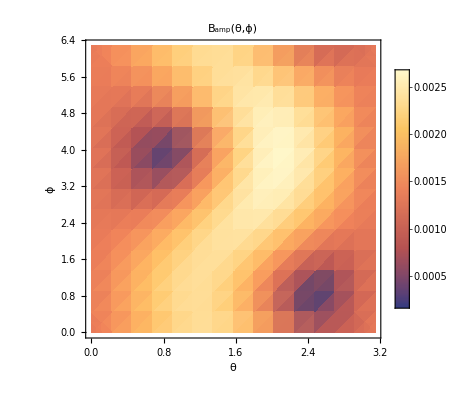

```mathematica
p2 = DensityPlot[plot1[θ,ϕ, bz, R, s, dz,dx,dy], {θ, 0, π},{ϕ, 0, 2π},Ticks->{Subdivide[0, π, 10], Automatic}, AxesLabel->{θ,ϕ},PlotRange->{{0,π}, Automatic}, PlotLabel->"B_amp(θ,ϕ)", PlotLegends->Automatic]
```

```mathematica
p2=DensityPlot[plot1[θ,ϕ,bz,R,s,dz,dx,dy],{θ,0,π},{ϕ,0,2 π},Ticks->{Table[{i,Row[{i/π,"π"}]},{i,0,2,1/2}],Automatic},AxesLabel->{"θ","ϕ"},PlotRange->{{0,π},Automatic},PlotLabel->"\!\(\*SubscriptBox[\(B\), \(amp\)]\)(θ,ϕ)",PlotLegends->Automatic]
```

-Graphics-

```mathematica
Export["Bamp_Vs_theta_phi_gen_dis_s0.1.pdf", p2]
```

Bamp_Vs_theta_phi_gen_dis_s0.1.pdf

```mathematica
R =40*10^-6;
dz=-389*10^-6;
dx=-389*10^-6;
dy=-389*10^-6 ;
s=-0.1 ;
bz=3.3;
```

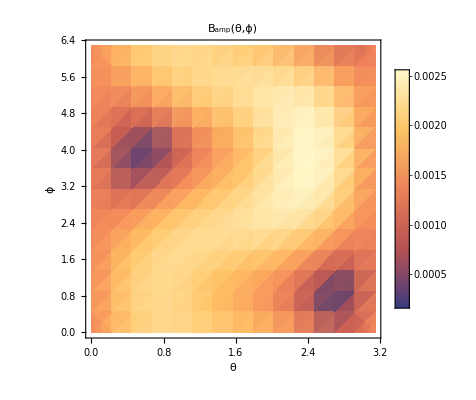

```mathematica
p3 = DensityPlot[plot1[θ,ϕ, bz, R, s, dz,dx,dy], {θ, 0, π},{ϕ, 0, 2π},Ticks->{Subdivide[0, π, 10], Automatic}, AxesLabel->{θ,ϕ, Subscript[B, amp]},PlotRange->{{0,π}, Automatic}, PlotLabel->"B_amp(θ,ϕ)", PlotLegends->Automatic]
```

```mathematica
Export["Bamp_Vs_theta_phi_gen_dis_s-0.1.pdf", p3]
```

Bamp_Vs_theta_phi_gen_dis_s-0.1.pdf

```mathematica
Export["Bamp_Vs_theta_phi_gen_dis.pdf", p1]
```

Bamp_Vs_theta_phi_gen_dis.pdf

# End of the Mathematica Notebook

## The next part for Force calculation is given in the notebook - “Force General Translation.nb”.